```mathematica
(*Load the finite element package*)
Needs["NDSolve`FEM`"];

(*Define parameters*)
omega=1;    (*Replace with your desired value*)
r=1;        (*Replace with your desired value*)
xMax=20;    (*Set the maximum x value*)
zMax=10;    (*Set the maximum z value*)
LD=1/omega;

(*Define the computational domain*)
region=Rectangle[{-xMax,0},{xMax,zMax}];

(*Define the PDE with NeumannValue terms included*)
pde=-Laplacian[C[x,z],{x,z}]+NeumannValue[omega*C[x,z]-r*UnitStep[-x],z==0]+NeumannValue[0,x==-xMax||x==xMax||z==zMax]==0;

(*Increase spatial resolution by refining the mesh*)
meshOptions={"MaxCellMeasure"->0.001};  (*Further decrease for finer mesh*)

(*Define the Analytical Solutions*)
CAnalytical[x_]:=Module[{nMax=150,sum=0},sum=Sum[Module[{kn=Pi (2 n+1)/(2 xMax)},(Sin[kn x] Cosh[kn zMax])/(kn (kn Sinh[kn zMax]+omega Cosh[kn zMax]))],{n,0,nMax}];
(r/(2 omega))-(r/xMax) sum];

CAnalyticApprox[x_]:=(r/omega)*(HeavisideTheta[-x]+(Cos[x/LD]/π) Sign[x] (π/2-SinIntegral[Abs[x]/LD])+(Sin[x/LD]/π) CosIntegral[Abs[x]/LD]);

CAnalyticlFF[x_]:=(r/omega)*(HeavisideTheta[-x]+LD/(π x));

CAnalyticlNF[x_]:=(r/(π omega))*(HeavisideTheta[-x]+Sign[x] (π/2-(x/LD))+(x/LD) (Log[Abs[x]/LD]+EulerGamma));
```

```mathematica
(*Generate x-values with higher density near x=0 using a Gaussian function*)(*First set of x-values*)
n1=60;                (*Total number of points for the first set*)
sigma1=xMax;         (*Standard deviation for the first set*)
uList1=Subdivide[0.001,0.999,n1];  (*Avoid extremes at 0 and 1*)
xList1=InverseCDF[NormalDistribution[0,sigma1],uList1];
xList1=Select[xList1,-xMax<=#<=xMax&&Abs[#]>10^-8&];  (*Limit to[-xMax,xMax],exclude x=0*)
xList1=Sort[xList1];

(*Second set of x-values*)
n2=40;                (*Total number of points for the second set*)
sigma2=xMax/10;         (*Standard deviation for the second set*)
uList2=Subdivide[0.00001,0.999,n2];  (*Avoid extremes at 0 and 1*)
xList2=InverseCDF[NormalDistribution[0,sigma2],uList2];
xList2=Select[xList2,-xMax<=#<=xMax&&Abs[#]>10^-8&];  (*Limit to[-xMax,xMax],exclude x=0*)
xList2=Sort[xList2];

(*Combine the two lists*)
xList=Join[xList1,xList2];
xList=Sort[xList];  (*Optional:Sort the combined list*)
xList=DeleteDuplicates[xList];  (*Optional:Remove duplicate values*)
```

```mathematica
(*Solve the PDE*)
solution=NDSolveValue[pde,C,{x,z}∈region,Method->{"FiniteElement","MeshOptions"->meshOptions}];
```

```mathematica
(*Compute solution values*)
solutionList=Reap[Do[Quiet[Check[With[{y=solution[x,0]-0.003},If[NumericQ[y],Sow[{x,y}]]],Null]],{x,xList}]][[2,1]];

(*Compute CAnalytical values*)
CAnalyticalList=Reap[Do[Quiet[Check[With[{y=CAnalytical[x]},If[NumericQ[y],Sow[{x,y}]]],Null]],{x,xList}]][[2,1]];

(*Compute CAnalyticApprox values*)
CAnalyticApproxList=Reap[Do[Quiet[Check[With[{y=CAnalyticApprox[x]},If[NumericQ[y],Sow[{x,y}]]],Null]],{x,xList}]][[2,1]];

(*x-values for CAnalyticlFF*)
xListFF=Select[xList,#>=xMax*0.45&];

(*Compute CAnalyticlFF values*)
CAnalyticlFFList=Reap[Do[Quiet[Check[With[{y=CAnalyticlFF[x]},If[NumericQ[y],Sow[{x,y}]]],Null]],{x,xListFF}]][[2,1]];

(*x-values for CAnalyticlNF*)
xListNF=Select[xList,0<=#<=xMax*0.075&];

(*Compute CAnalyticlNF values*)
CAnalyticlNFList=Reap[Do[Quiet[Check[With[{y=CAnalyticlNF[x]},If[NumericQ[y],Sow[{x,y}]]],Null]],{x,xListNF}]][[2,1]];

(*Combine datasets*)
datasets={solutionList,CAnalyticalList,CAnalyticApproxList,CAnalyticlFFList,CAnalyticlNFList};
```

```mathematica
plot1D=ListPlot[datasets,Joined->False,(*No lines connecting the markers*)PlotRange->All,FrameLabel->{Style["x",FontFamily->"Helvetica Neue",FontSize->22,FontColor->Black],Style["c(x,0)",FontFamily->"Helvetica Neue",FontSize->22,FontColor->Black]},PlotStyle->{{Black},(*Numerical:Black*){Red},(*Analytical:Red*){Blue},(*Approx.Analytical:Blue*){Purple},(*CAnalyticlFF:Purple*){Green}  (*CAnalyticlNF:Green*)},
PlotMarkers->{
{Graphics[{EdgeForm[{Black,AbsoluteThickness[2]}],Disk[]}],16},(*Hollow Circle*)
{Graphics[{EdgeForm[{Red,AbsoluteThickness[2]}],FaceForm[None],Rectangle[]}],16},(*Hollow Square*)
{Graphics[{EdgeForm[{Blue,AbsoluteThickness[2]}],FaceForm[None],Triangle[]}],16},(*Hollow Triangle*)
{Graphics[{EdgeForm[{Green,AbsoluteThickness[2]}],FaceForm[None],RegularPolygon[5]}],16},(*Hollow Pentagon*){Graphics[{EdgeForm[{Cyan,AbsoluteThickness[2]}],FaceForm[None],RegularPolygon[5]}],16}   (*Hollow Pentagon*)},
PlotLegends->Placed[PointLegend[
{
Graphics[{EdgeForm[{Black,AbsoluteThickness[2]}],Disk[]}],
Graphics[{EdgeForm[{Red,AbsoluteThickness[2]}],FaceForm[None],Rectangle[]}],
Graphics[{EdgeForm[{Blue,AbsoluteThickness[2]}],FaceForm[None],Triangle[]}],
Graphics[{EdgeForm[{Green,AbsoluteThickness[2]}],FaceForm[None],RegularPolygon[5]}],
Graphics[{EdgeForm[{Cyan,AbsoluteThickness[2]}],FaceForm[None],RegularPolygon[5]}]
},
{"Numerical Solution","Eq. S11","Eq. S12","Eq. S13","Eq. S14"},LabelStyle->{FontFamily->"Helvetica Neue",FontSize->14},LegendMarkerSize->{40,15}],{0.8,0.85}],GridLines->Automatic,ImageSize->800,BaseStyle->{FontFamily->"Helvetica Neue",FontSize->14},Frame->True,FrameStyle->Directive[GrayLevel[0],13,FontFamily->"Helvetica Neue",AbsoluteThickness[1.0]],FrameTicks->Automatic];
```

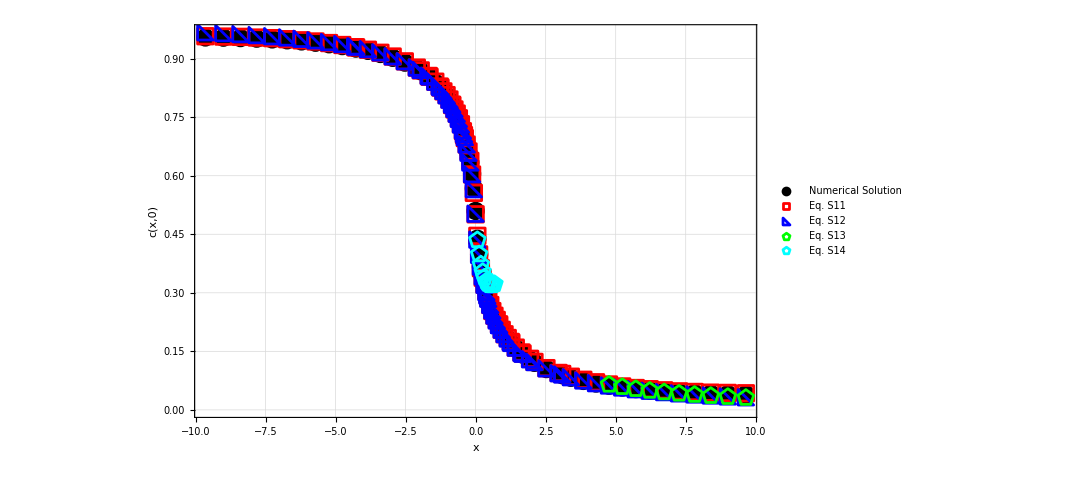

```mathematica
(*Display the plot*)
plot1D
```

```mathematica
Export["1Dplot.png", plot1D, ImageResolution->600]
```

1Dplot.png

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["1Dplot.png"]]]
```

```mathematica
(*---Begin Additional Code for Bar1 and Bar1' Plot---*)(*Define Bar1[x]*)
Bar1[x_]:=HeavisideTheta[-x]*(2*CAnalytical[x]-r/omega)

λa := 1/LD

(*Define S18 (|x| >>λa limit)*)
S18[x_]:=(r/omega)*HeavisideTheta[-x]*(1+2λa/(Pi*x)) + 0.01

(*Define S19 (|x|<<λa limit)*)
S19[x_]:=(r/omega)*HeavisideTheta[-x]*(2x/(Pi*λa))*(Log[Abs[x]/λa]+EulerGamma-1)

(*Generate x-values for Bar1 and Bar1' with high resolution*)
xListBar=Subdivide[-xMax,xMax,150];
xListSparse=Subdivide[-xMax,xMax,50];
xListDense=Subdivide[-xMax/5,0,200];
```

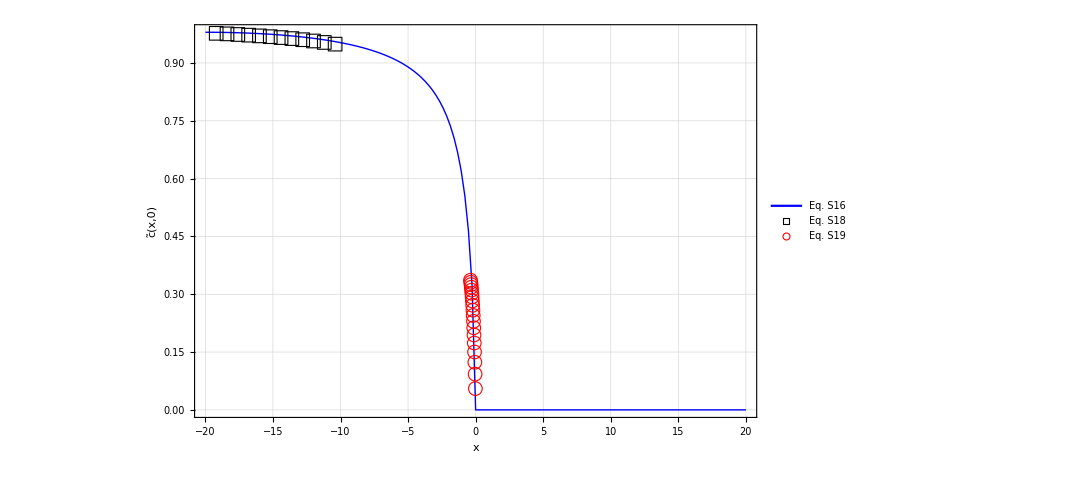

BarPlot_Combined.png

```mathematica
(*Compute Bar1[x] values*)
Bar1List=Reap[Do[Quiet[Check[With[{y=Bar1[x]},If[NumericQ[y],Sow[{x,y}]]],Null]],{x,xListBar}]][[2,1]];

(*Compute S18 values for x>6*)
S18List=Reap[Do[Quiet[Check[With[{y=S18[x]},If[NumericQ[y]&&-xMax<x<-xMax+10,Sow[{x,y}]]],Null]],{x,xListSparse}]][[2,1]];

(*Compute S19 values*)
S19List=Reap[Do[Quiet[Check[With[{y=S19[x]},If[NumericQ[y]&&0>x>-0.4,Sow[{x,y}]]],Null]],{x,xListDense}]][[2,1]];

plotCombined=ListPlot[{Bar1List,(*Eq.S16*)S18List,(*Eq.S18*)S19List    (*Eq.S19*)},Joined->{True,False,False},PlotStyle->{Directive[Blue,Thick],(*Solid blue line for Bar1List*)Black,(*Black circles for S18List*)Red                     (*Red squares for S19List*)},PlotMarkers->{None,(*No markers for Bar1List since it's a line*){Graphics[{EdgeForm[{Black,Thick}],FaceForm[None],Rectangle[]}],14},(*Black circles for S18List*){Graphics[{EdgeForm[{Red,Thick}],FaceForm[None],Disk[]}],14}     (*Red squares for S19List*)},PlotLegends->Placed[LineLegend[{Style["Eq. S16",Blue,Thick,Black],(*Added Black color*)Style["Eq. S18",Black,Black],(*Ensured Black color*)Style["Eq. S19",Red,Black]           (*Added Black color to text*)},LegendMarkerSize->{40,15},LabelStyle->{FontFamily->"Helvetica Neue",FontSize->14,FontColor->Black} (*Set Legend Label FontColor to Black*)],{0.8,0.85} (*Position of the legend*)],PlotRange->All,Frame->True,FrameLabel->{Style["x",FontFamily->"Helvetica Neue",FontSize->22,FontColor->Black],Style[Overscript[c,"~"][x,0],FontFamily->"Helvetica Neue",FontSize->22,FontColor->Black] (*Updated label with Overtilde*)},GridLines->Automatic,ImageSize->800,BaseStyle->{FontFamily->"Helvetica Neue",FontSize->14,FontColor->Black},(*Set BaseStyle FontColor to Black*)FrameStyle->Directive[GrayLevel[0],13,FontFamily->"Helvetica Neue",AbsoluteThickness[1.0]],FrameTicks->Automatic];

(*Display the Combined Plot*)
plotCombined

(*Export the Combined Plot as a PNG file*)
Export["BarPlot_Combined.png",plotCombined,ImageResolution->800]
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["BarPlot_Combined.png"]]]
```